Количество точек: 49

UFL: 1/2

OFL: 15/4

EpsM: 1/16

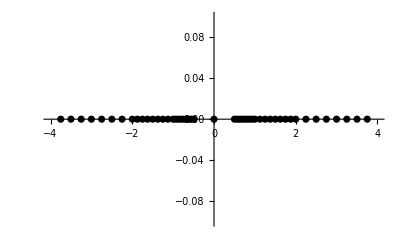

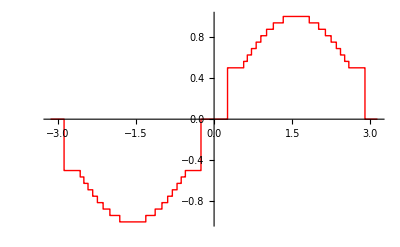

```mathematica
mlen=3;
a={-1,0,1};
mantiss=Range[1,2-1/2^mlen,1/2^mlen];
allNumbers=Union[Flatten[Outer[Times,mantiss,2^a]]];
allNumbersSigned=Union[Flatten[{allNumbers,-allNumbers,{0}}]];
UFL=Min[Select[allNumbersSigned,#>0&]];OFL=Max[allNumbersSigned];
EpsM=(Min[Select[allNumbersSigned,#>1&]]-1)/ 2;
Print["Количество точек: ",Length[allNumbersSigned]];
Print["UFL: ",UFL];
Print["OFL: ",OFL];
Print["EpsM: ",EpsM];
ListPlot[Table[{x,0},{x,allNumbersSigned}], PlotStyle->{Black}, PlotRange->{{-4,4},{-0.1,0.1}},Axes->{True,False}]
RoundModel[x_]:=First@Nearest[allNumbersSigned,x];
f[x_]:=RoundModel[Sin[x]];
ListPlot[Table[{x,f[x]},{x,- Pi, Pi,0.01}],Joined->True,InterpolationOrder->0,PlotStyle->{Red,Thick}]
```